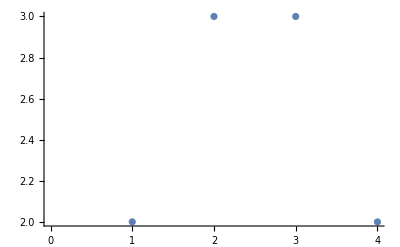

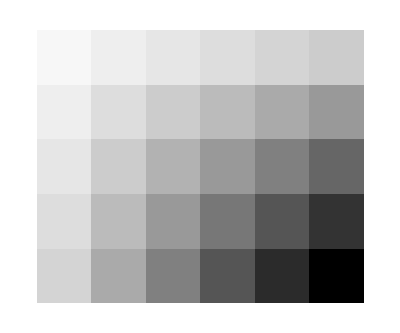

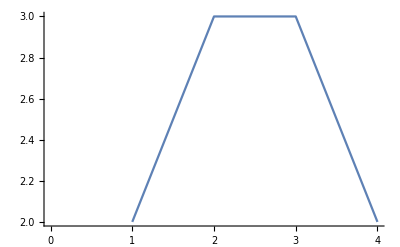

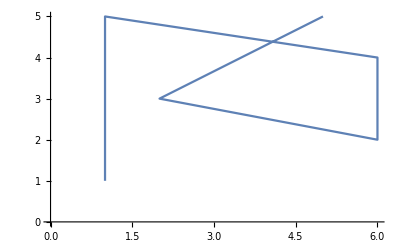

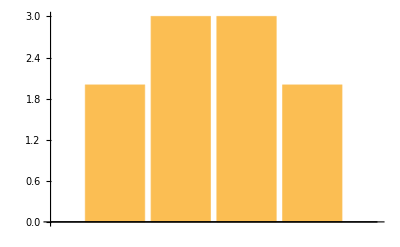

-Graphics-

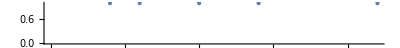

2
3
3

{-Graphics-,-Graphics-}

-Graphics3D-

```mathematica
ListPlot[{2,3,3,2}]
ArrayPlot[Table[x*y,{x,5},{y,6}]]
ListLinePlot[{2,3,3,2}]
ListLinePlot[{{1,1},{1,5},{6,4},{6,2},{2,3},{5,5}}]
BarChart[{2,3,3,2}]
PieChart[{2,3,3,2}]
NumberLinePlot[{2,3,5,7,11}]
Column[{2,3,3}]
{PieChart[Range[3]], PieChart[Range[5]]}
Plot3D[Sin[y+Sin[3*x]], {x,-3,3},{y,-3,3}]
```





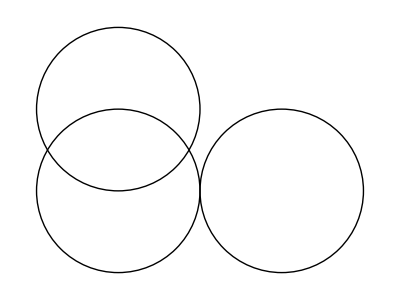

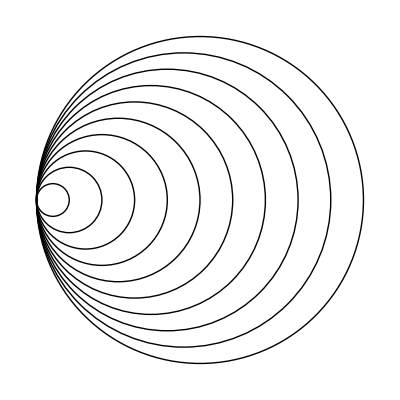

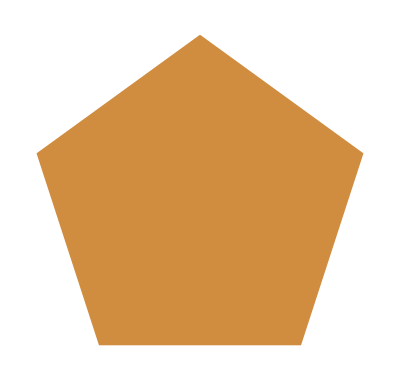
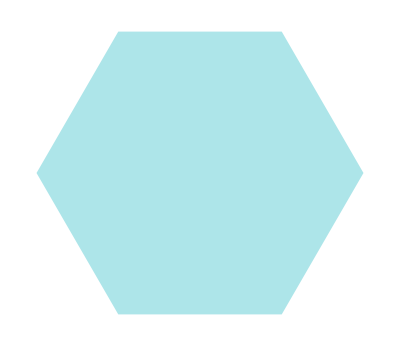
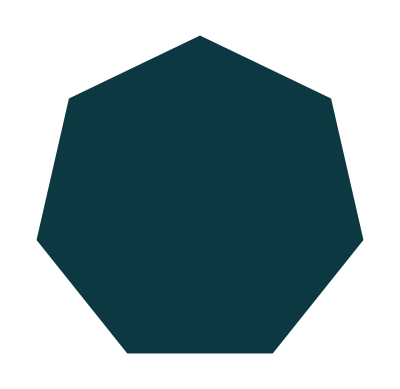
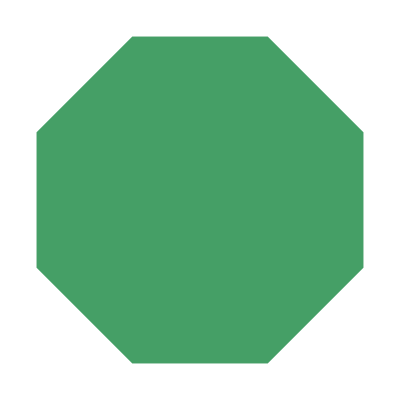
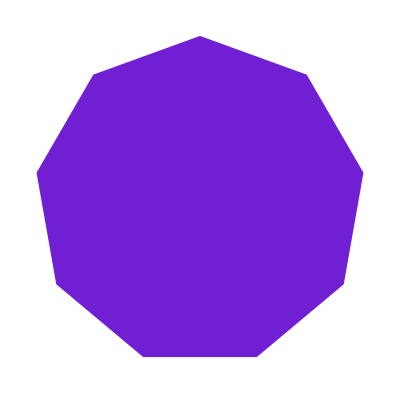
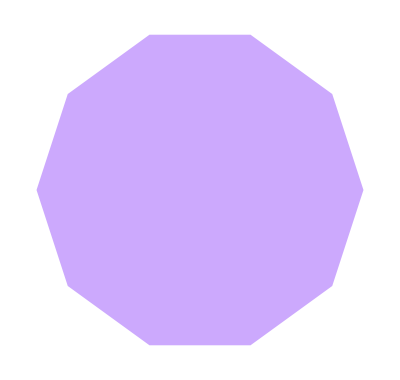

```mathematica
Graphics[Circle[]]
Graphics[Disk[]]
Graphics[{Circle[{1,1}],Circle[{1,2}],Circle[{3,1}]}]
Graphics[Table[Circle[{x,0},x],{x,10}]]
Table[Graphics[Style[RegularPolygon[x],RandomColor[]]],{x,5,10}]
```

```mathematica
Graphics3D[Sphere[]]
Graphics3D[Cone[]]
Graphics3D[Cylinder[]]
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Manipulate[Table[Orange,n],{n,1,5,1}]
Manipulate[Column[{n,n^2,n^3}],{n,1,10}]
Manipulate[BarChart[{Sin[x],Cos[x],Sqrt[2]-Sin[x]-Cos[x],Sqrt[2]}],{x,0,Pi/2,0.01}]
Manipulate[Part[{2,2,4},x],{x,1,3,1}]
Manipulate[RandomInteger[n],{n,4,5,1}]
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Sphere[{x,0,0}],Opacity[o]]}],{x,1,3},{o,0.5,1}]
```

```mathematica
(*curImage=CurrentImage[]*)
(*ColorNegate[curImage]
ImageCollage[Table[Blur[curImage,x],{x,0,15,5}]]*)
(*DominantColors[curImage]
Binarize[curImage]
DominantColors[Binarize[curImage]]*)
(*EdgeDetect[curImage]
ImageAdd[curImage,EdgeDetect[curImage]]
Manipulate[Binarize[curImage,x],{x,0,1}]*)
```

```mathematica
ExampleData[{"TestImage","Mandrill"}]
(*WikipediaData["crocodiles","ImageList"]*)
```

-Graphics-

{{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{0,0,1,1,1,1,0},{0,0,1,1,1,1,0},{0,0,1,1,1,1,0},{0,0,1,0,1,1,0},{1,0,1,0,0,0,0},{1,0,0,1,0,0,0},{1,0,0,1,0,0,0},{1,0,0,1,0,0,0},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}}

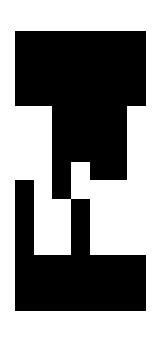

```mathematica
tmp1=ImageData[Binarize[Rasterize["W"]]]
ArrayPlot[tmp1]
```

{1→2,2→3,3→4,4→1,3→1,2→2,2→2}

{1→1,1→2,1→3,1→4,1→5,1→6,2→1,2→2,2→3,2→4,2→5,2→6,3→1,3→2,3→3,3→4,3→5,3→6,4→1,4→2,4→3,4→4,4→5,4→6,5→1,5→2,5→3,5→4,5→5,5→6,6→1,6→2,6→3,6→4,6→5,6→6}

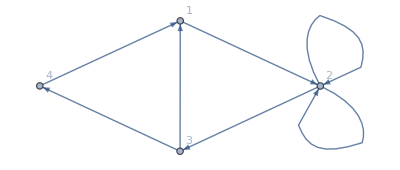

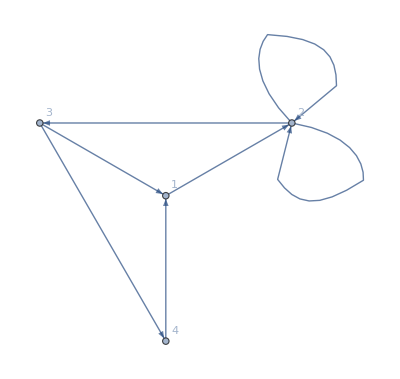

{4,1,2}

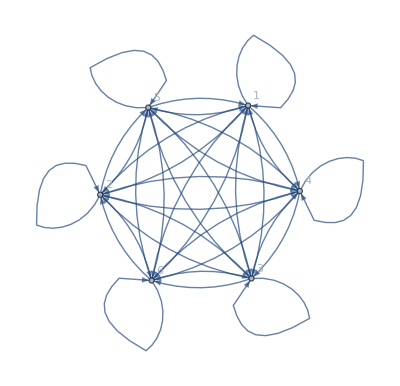

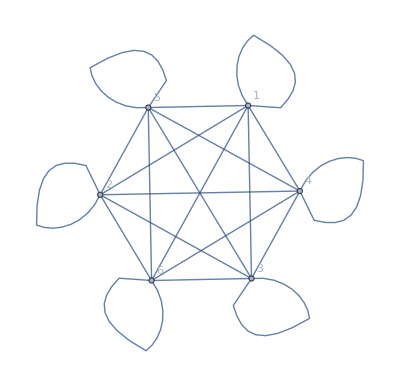

-Graphics-

```mathematica
z1={1->2,2->3,3->4,4->1,3->1,2->2,2->2}
z2 = Flatten[Table[x->y,{x,6},{y,6}]]
Graph[z1,VertexLabels->All]
Graph[z1,VertexLabels->All,GraphLayout->"RadialEmbedding"]
FindShortestPath[Graph[z1],4,2]
Graph[z2,VertexLabels->All]
UndirectedGraph[z2,VertexLabels->All]
CommunityGraphPlot[Graph[Table[RandomInteger[10]->RandomInteger[10],20]]]
```

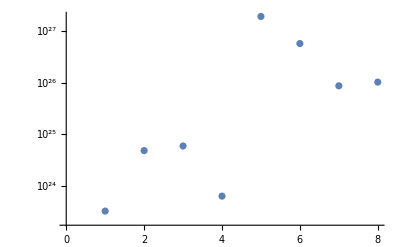

```mathematica
ListLogPlot[EntityClass["Planet",All]["Mass"]]
```

{{1,3,4,3,1,2},{2,2,4,5,7,6,8}}

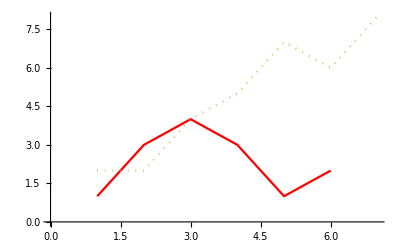

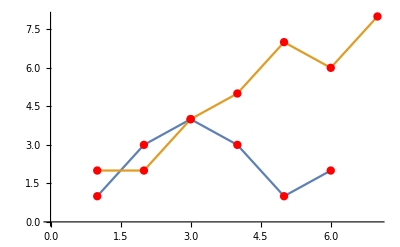

```mathematica
z1={{1,3,4,3,1,2},{2,2,4,5,7,6,8}}
ListLinePlot[z1,PlotStyle->{Red,Dotted}]
ListLinePlot[z1,Mesh->All,MeshStyle->Red]
```

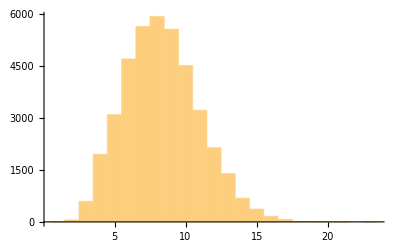

```mathematica
Histogram[StringLength[WordList[]]]
```

```mathematica
Clear[z1]
z1=Framed[233,Background->LightYellow,FrameStyle->LightGray]
Labeled[z1,Style["233",Italic,Orange]]
```

233

233233

-Graphics-

-Graphics-

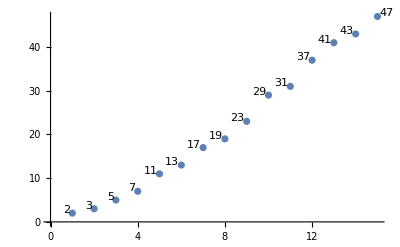

-Graphics-

-Graphics-

-Graphics-

```mathematica
PieChart[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Red],Labeled[4,Orange],2,2}]
ListPlot[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Pink],Labeled[4,Yellow],5,6,7}]
ListPlot[Table[Labeled[Prime[n],Prime[n]],{n,15}]]
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
PieChart[{Style[3,Red],Style[2,Green],Style[1,Yellow],1,2}]
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
PieChart[{1->"one",2->"two",3->Blue,4->Red}]
```